# IX1501 HT23 Project 1

Course code: IX1501
Date: 2023-09-04

Samir Alami, samirala@kth.se
Ali Sahibi, sahibi@kth.se

Probability distribution of a sum of independent random variables

## Summary

### Task

-Graphics-
At a dice game you throw five dice in the form of the Platonic Solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. You win the game if the sum of the numbers S satisfies S≤10 or S≥45. Note that S is an integer value ranging between 5 and 50.

Your task is as follows:

By means of the discrete convolution method,
Task 1: Determine the probability function of S. Express it as a form of a table.
Task 2: Determine the probability of winning the game.

By means of the Monte Carlo simulation,
Task 3: Obtain the probability of winning the game with 1000 trials.
Task 4: Discuss how the probability changes when the number of trials changes from a small number (e.g., 10) to a large number (e.g., 100000). Provide a figure with the discussion.
Task 5: How many trials are needed to keep the relative error between the exact value and the simulation result less than 10%? Provide your reasoning.

### Result

Determine the probability function of S. Express it as a form of a table.

"S" | "P(S=s)"
5 | 1/46080
6 | 1/9216
7 | 1/3072
8 | 7/9216
9 | 23/15360
10 | 121/46080
11 | 97/23040
12 | 29/4608
13 | 409/46080
14 | 61/5120
15 | 707/46080
16 | 293/15360
17 | 53/2304
18 | 311/11520
19 | 95/3072
20 | 1597/46080
21 | 39/1024
22 | 379/9216
23 | 1007/23040
24 | 211/4608
25 | 1091/23040
26 | 223/4608
27 | 1127/23040
28 | 1127/23040
29 | 223/4608
30 | 1091/23040
31 | 211/4608
32 | 1007/23040
33 | 379/9216
34 | 39/1024
35 | 1597/46080
36 | 95/3072
37 | 311/11520
38 | 53/2304
39 | 293/15360
40 | 707/46080
41 | 61/5120
42 | 409/46080
43 | 29/4608
44 | 97/23040
45 | 121/46080
46 | 23/15360
47 | 7/9216
48 | 1/3072
49 | 1/9216
50 | 1/46080

Determine the probability of winning the game.
41/3840

Obtain the probability of winning the game with 1000 trials.
11/1000

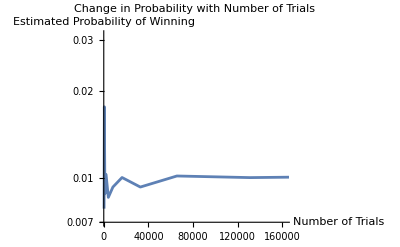
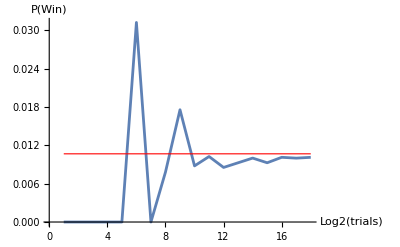
Discuss how the probability changes with the number of trials and provide a figure.

The idea behind a Monte Carlo simulation is to approximate the probability of a certain event rather than mathematically evaluate it. This can be useful if the evaluation is complex or difficult, or if one simply does not know how to evaluate it. The accuracy of the probability approximation increases as the number of trials increases. And as the number of trials become arbitrarily large N-> ∞  then P_montecarlo=P, the approximation will equal the actual probability.

To investigate how the probability changes with different numbers of trials, we can repeat Task 3 with varying numbers of trials , 2 to 2^18 and observe the results. 

Below is a plot of the probability estimation with increasing number of trials. 
-Graphics-
Below is another plot. But it is instead of how the probability estimation changes with log_2(number of trials). The red line is the actual probability value as calculated in task 2. 
-Graphics-
As can be seen by the plots with increasing number of trials we get an increasingly accurate probability estimation, As expected by a Monte Carlo simulation.

Determine the number of trials needed to keep the relative error below 10%. Provide reasoning.

The Monte Carlo principle can be described as:

If N is the size of the sample space, number of simulations, and m is the number of simulations that satisfy a certain condition C. And if we know the true probability of C. Then P(C)≈ m/N and if N->∞ then P(C)=m/N.

The relative error value can be described as: E=|P(C) -m/N| / P(C). This implies that if N->∞ then E=|P(C) - P(C)|/P(C)=0. Thus the relative error decreases as the number of simulations increases. 

To find an exact number of trials which will satisfy that the relative error is less than 10% is impossible, the number of trials will vary since the trials are random. Only scenario where you can guarantee it is less than 10% is when N->∞. However we can try to find the number of trials which will with high probability give us a relative error rate that is less than 10%.

We approximated the on average number of trials required to satisfy the error rate condition, that number is 2228. This tells us that on average across multiple Monte Carlo simulations, it will require about 2228 trials to get an error rate condition less than 10%.  

The we approximated the probabilities of a relative error rate of less than 10% for different number of trials. Below are the results: 
"trials" | "TraditionalForm`P(relative\ error\  < \ 10)"
1000 | "27%"
2228 | "41%"
5000 | "53%"
10000 | "62%"
20000 | "85%"
46080 | "99%"

As we can see the on average 2228 trials required before a Monte Carlo simulation has a relative error rate of less than 10% has a quite poor probability of having an error rate of less than 10% at 41%. The number of required trials to get a satisfying error rate with high probability (>=99%) is 46080, which is interesting since that is the number of possible outcomes when throwing 5 platonic solids.

## Method

### Task 1: Determine the probability function of S

We will first define the probability distributions for each of the Platonic Solids. We will assume that each die is fair, meaning that each outcome is equally likely. Here are the probability distributions for each die:

Tetrahedron (4-sided die)
	Probability of each outcome (1 to 4) is 1/4.

Hexahedron (6-sided die)
	Probability of each outcome (1 to 6) is 1/6.

Octahedron (8-sided die)
	Probability of each outcome (1 to 8) is 1/8.

Dodecahedron (12-sided die)
	Probability of each outcome (1 to 12) is 1/12.

Icosahedron (20-sided die)
	Probability of each outcome (1 to 20) is 1/20.

Now, we can calculate the convolution of these probability distributions to find the probability distribution of the sum S.

### Task 2: Determine the probability of winning the game

To determine the probability of winning the game, we need to sum the probabilities of all values of S where S <= 10 or S >= 45.

### Task 3: Obtain the probability of winning the game with 1000 trials (Monte Carlo simulation)

In this task, we will simulate throwing the five Platonic Solid dice 1000 times and calculate the proportion of simulations where we win. The steps are as follows:

Simulate rolling each of the five dice in each trial and calculate the sum S for each trial.

Count the number of trials where S satisfies the winning condition (S <= 10 or S >= 45).

Calculate the probability of winning as the ratio of the number of winning trials to the total number of trials (1000 in this case).

### Task 4: Discuss how the probability changes with the number of trials and provide a figure.

To observe how the probability changes with the number of trials, we can perform the simulation for various numbers of trials, ranging from a small number, 2, to a large number, 2^18. Then we can create a plot to visualize this change.

### Task 5: Determine the number of trials needed to keep the relative error below 10%. Provide reasoning.

To determine the number of trials needed to achieve a relative error value below 10% between the exact probability and the simulation probability, we can perform Monte Carlo simulations with increasing numbers of trials until we get a relative error value that is less than 10%. Since the simulation result can vary, the aforementioned test  is repeated a number of times so that we calculate the average number of trials required to get a relative error value that is less than 10%. 

We also analyze the probability of getting an error value less than 10% for different number of trials, this is done by picking a trial number to use for the Monte Carlo simulation and then repeating the simulation a certain amount of times while keeping track of the number of simulation that satisfies our condition. By doing this we approximate the probability of the a relative error rate of less than 10% for different number of trials.

## Code

### Task 1: Determine the probability function of S

Define the probability distributions for each die

```mathematica
probabilitiesTetrahedron=Table[1/4,{i,1,4}];
probabilitiesHexahedron=Table[1/6,{i,1,6}];
probabilitiesOctahedron=Table[1/8,{i,1,8}];
probabilitiesDodecahedron=Table[1/12,{i,1,12}];
probabilitiesIcosahedron=Table[1/20,{i,1,20}];
```

Convolve the probability distributions to get the probability distribution of S

```mathematica
convolvedDistribution1=ListConvolve[probabilitiesTetrahedron,probabilitiesHexahedron,{1,-1},0];
convolvedDistribution2=ListConvolve[probabilitiesOctahedron,probabilitiesDodecahedron, {1,-1},0];
convolvedDistributionComb=ListConvolve[convolvedDistribution1,convolvedDistribution2,{1,-1},0];
totalPdf=ListConvolve[convolvedDistributionComb,probabilitiesIcosahedron,{1,-1},0];
```

Create a table of probabilities for each possible sum S

```mathematica
probabilityTable=Table[{s,totalPdf[[s-4]]},{s,5,50}];
```

Display the probability table

```mathematica
TableForm[probabilityTable,TableHeadings->{None,{"S","P(S=s)"}}]
```

S | P(S=s)
5 | 1/46080
6 | 1/9216
7 | 1/3072
8 | 7/9216
9 | 23/15360
10 | 121/46080
11 | 97/23040
12 | 29/4608
13 | 409/46080
14 | 61/5120
15 | 707/46080
16 | 293/15360
17 | 53/2304
18 | 311/11520
19 | 95/3072
20 | 1597/46080
21 | 39/1024
22 | 379/9216
23 | 1007/23040
24 | 211/4608
25 | 1091/23040
26 | 223/4608
27 | 1127/23040
28 | 1127/23040
29 | 223/4608
30 | 1091/23040
31 | 211/4608
32 | 1007/23040
33 | 379/9216
34 | 39/1024
35 | 1597/46080
36 | 95/3072
37 | 311/11520
38 | 53/2304
39 | 293/15360
40 | 707/46080
41 | 61/5120
42 | 409/46080
43 | 29/4608
44 | 97/23040
45 | 121/46080
46 | 23/15360
47 | 7/9216
48 | 1/3072
49 | 1/9216
50 | 1/46080

### Task 2: Determine the probability of winning the game

Calculate the probability of winning the game

```mathematica
winningProbability=Total[Select[probabilityTable,#[[1]]<=10||#[[1]]>=45&][[All,2]]];
```

The variable winningProbability now contains the probability of winning the game. We can evaluate this code to get the result.

```mathematica
winningProbability
```

41/3840

### Task 3: Obtain the probability of winning the game with 1000 trials (Monte Carlo simulation)

For this task, we’ll use Monte Carlo simulation to estimate the probability of winning the game with 1000 trials. We’ll simulate the rolling of five dice and count how many times we win.

```mathematica
numTrials=1000;
winCount=0;

For[i=1,i<=numTrials,i++,diceRolls=RandomInteger[{1,4},1]~Join~RandomInteger[{1,6},1]~Join~RandomInteger[{1,8},1]~Join~RandomInteger[{1,12},1]~Join~RandomInteger[{1,20},1];
totalSum=Total[diceRolls];
If[totalSum<=10||totalSum>=45,winCount++];]

estimatedProbability=winCount/numTrials
```

1/100

expectedInvestment=expectedWin*2 //N

### Task 4: Discuss how the probability changes with the number of trials and provide a figure.

To analyze how the probability changes with the number of trials, we can perform simulations for various trial numbers such as 2 to 2^18 and observe the trend. We’ll create a plot to visualize this change.

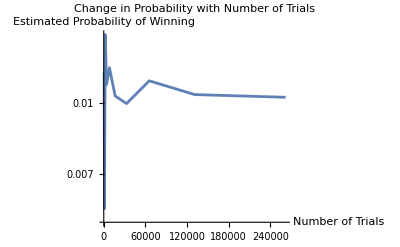

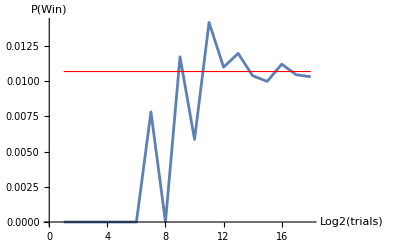

```mathematica
randSum := Total[#]&/@{ RandomInteger[{1,#}]& /@ {4,6,8,12,20}};

Nwins[samples_]:= Module[{s=samples,wins=0, curr=0},For[i = 1, i<= s, i++, curr=randSum[[1]];If[curr <= 10 || curr >= 45,wins++]]; Return[<|"wins"->wins, "probability"->N[wins/samples]|>]];

trialCounts=Table[2^i,{i,1,18}];
estimatedProbabilities=Nwins[#][["probability"]]&/@trialCounts;

listlog=ListLogPlot[Transpose[{trialCounts,estimatedProbabilities}],Joined->True,AxesLabel->{"Number of Trials","Estimated Probability of Winning"},PlotLabel->"Change in Probability with Number of Trials"]

probabilityplot=Plot[winningProbability,{i,1,18},PlotStyle->{Red,Thickness[0.002]}];

log2Transform = {Log2[#[[1]]], #[[2]]}&/@ Table[{trialCounts[[i]],estimatedProbabilities[[i]]},{i,1,Length[trialCounts]}];
log2plot=ListPlot[log2Transform, Joined->True, AxesLabel->{"Log2(trials)","P(Win)"}];

Show[log2plot,probabilityplot]
```

### Task 5: Determine the number of trials needed to keep the relative error below 10%. Provide reasoning.

To determine the number of trials needed to keep the relative error below 10%, we can iterate through different trial numbers and stop when the relative error is less than 10%. We can than repeat this a certain amount of times, 1000 in our case, to get an average of the number of trials needed to get a relative error value below 10%.

```mathematica
desiredRelativeError=0.1; (*Desired relative error threshold*)
numTrials=2; (*Initial number of trials*)

(*Initialize a variable to store the relative error*)
relativeError=1.0;

relativeErr[Pm_]:=Abs[winningProbability - Pm]/winningProbability;

repeats = 1000;
totalTrials = 0;
totalRelativeError = 0;
For[j=1,j<=repeats,j++,
numTrials = 2;
relativeError=1.0;
While[relativeError > desiredRelativeError,
	res = Nwins[numTrials];
	relativeError = relativeErr[res[["probability"]]];
	numTrials *= 2
];

totalTrials = (totalTrials+(numTrials/2));
totalRelativeError = (totalRelativeError + relativeError);

];
avgTrials = totalTrials/repeats;
avgRelativeError=totalRelativeError/repeats;
```

The above code snippet will keep doubling the number of trials until the relative error falls below 10%.

```mathematica
numTrials
relativeError
N[avgTrials]
avgRelativeError
```

2048

0.00609756

2228.22

0.0752308

```mathematica
nTrials = Floor[avgTrials]
```

2228

```mathematica
Nwins[nTrials]
```

<|wins→28,probability→0.0125673|>

This function performs the monte Carlo simulation for a certain number of trials and then checks if the relative error is less than 10%. It does so repeatedly a certain amount of times, 100, and keeps track of the number of simulations which satisfies our condition. Using this data we can approximate the probability of getting a relative error less than 10% for a certain number of trials in the Monte Carlo simulation.

```mathematica
Pf[trials_,iters_]:=Module[{max=iters,prob0=0,err=0, condMet=0},
For[j=1, j<= max, j++, 
prob0=Nwins[trials][["probability"]];
err=relativeErr[prob0];
If[err<desiredRelativeError,condMet++];
];Return [condMet/max]];
```

We use the Pf function on a few number of possible trials to see probability for different number of trials to have a relative error less than 10%.

```mathematica
plist={#,Pf[#,100]} &/@{1000, nTrials, 5000,10000,20000,4*6*8*12*20}
```

{{1000,27/100},{2228,41/100},{5000,53/100},{10000,31/50},{20000,17/20},{46080,99/100}}

```mathematica
plistfiltered=({#[[1]],PercentForm[N[#[[2]]]]})&/@plist
```

{{1000,27%},{2228,41%},{5000,53%},{10000,62%},{20000,85%},{46080,99%}}

```mathematica
Grid[Prepend[plistfiltered,{"trials","TraditionalForm`P(relative\ error\  < \ 10)"}],Frame->All]
```

trials | TraditionalForm`P(relative\ error\  < \ 10)
1000 | 27%
2228 | 41%
5000 | 53%
10000 | 62%
20000 | 85%
46080 | 99%

The final value of numTrials will give you an estimate of how many trials are needed to achieve this level of accuracy.